```mathematica
CuriousQ[n_]:=n>2 && n==Total[Map[Factorial,IntegerDigits[n]]]
```

```mathematica
CuriousQ[145]
```

True

What is the maximum possible curious number?

We know that

```mathematica
9!
```

362880

So the maximum "curious total" for an n digit number is

```mathematica
CuriousMax[n_]:=9!*n;
```

The minimum value for an n digit number is

```mathematica
ValueMinN[n_]:=10^(n-1)
```

Is there a number of digits n when the minimum value of the number is certain to be higher than the maximum curious total of the number?

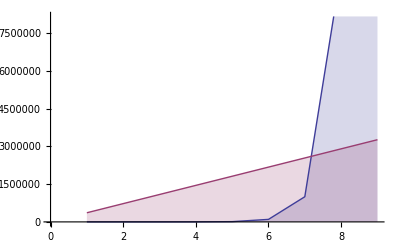

```mathematica
DiscretePlot[{ValueMinN[n],CuriousMax[n]},{n,1,9},Joined->True]
```

```mathematica
ValueMinN[8]
```

10000000

```mathematica
CuriousMax[8]
```

2903040

So there are no "curious" numbers with 8 or more digits, since the curious total will be less than the value of the number.

So we can see that all the curious numbers are less than 10^8-1

```mathematica
curiousUpperBound = CuriousMax[7]
```

2540160

We wish to find the sum of all curious numbers. So

```mathematica
Total[Select[Range[1,curiousUpperBound+1],CuriousQ]]
```

40730